## Ground state energy vs Cylindrical Well radius & ψ_1,ψ_2

```mathematica
ClearAll["Global`*"]
x=0.2;
hom=7.62559/0.067;(*ℏ^2/m^* for GaAs in eV A^2*)
vmax=0.67*1.247x; (*Diff in conduction band between GaAs and Subscript[Ga, 1-x] Subscript[Al, x] As*)
rw=Range[30.,300.,10.];(*Radius of well*)
energy=ConstantArray[{0.,0.,0},{Length[rw]}];
functions={0,0};

Do[
npwell = Floor[rw⟦m⟧/dr]; (*number of points in the inner radius*)
dr=1.;rmin=0.;rmax=rw⟦m⟧+200.;
r=Range[rmin,rmax,dr];lr=Length[r];
ψ=0.*r;v=ConstantArray[vmax,lr];
v⟦Range[npwell]⟧=0.;
ψ⟦1⟧=ψ⟦2⟧=1;
ϵ=0.0;dϵ=0.1;ψmax=2.;

Do[
ϵ=energy⟦m,k⟧+0.001;dϵ=0.001;
i=2;ψl=ψ⟦i⟧;
While[Abs[ψ⟦i⟧]<ψmax && i< lr,
ψ⟦i+1⟧=1/(2r⟦i⟧+dr)*(2r⟦i⟧*ψ⟦i⟧(2*dr^2*(v⟦i⟧-ϵ)/hom+2)+(-2r⟦i⟧+dr)*ψ⟦i-1⟧);i++];

ψl=ψ⟦i⟧;ϵ +=dϵ;

While[Abs[dϵ]>10^-12,
ψ=0.*r;
ψ⟦{1,2}⟧={1,1};
i=2;

While[Abs[ψ⟦i⟧]<ψmax && i< lr,
ψ⟦i+1⟧=1/(2r⟦i⟧+dr)*(2r⟦i⟧*ψ⟦i⟧(2*dr^2*(v⟦i⟧-ϵ)/hom+2)+(-2r⟦i⟧+dr)*ψ⟦i-1⟧);i++];
If[ψ⟦i⟧*ψl<0,dϵ=-dϵ/2.];
ψl=ψ⟦i⟧;ϵ+=dϵ];

energy⟦m,k+1⟧=ϵ-dϵ;
If[rw⟦m⟧==300. ,functions⟦k⟧=ψ/(√((√r*ψ).(√r*ψ) dr));]
,{k,2}];

,{m,Length[rw]}]
```

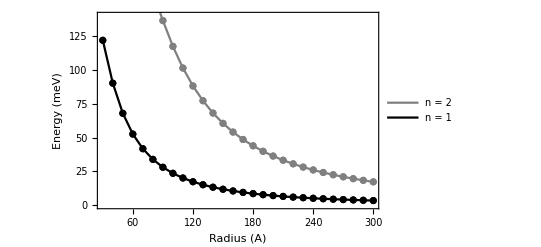

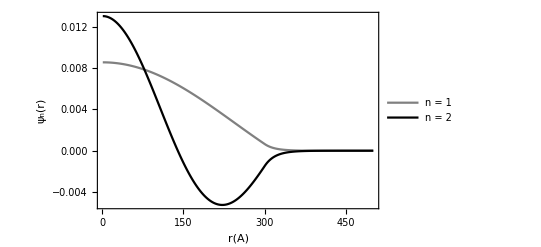

```mathematica
Show[
ListPlot[Table[{rw⟦i⟧,1000*energy⟦i,3⟧},{i,Length[rw]}],PlotStyle-> Gray,Joined->True,Mesh->Full,PlotLegends->{"n = 2"}],
ListPlot[Table[{rw⟦i⟧,1000*energy⟦i,2⟧},{i,Length[rw]}],PlotStyle-> Black,Joined->True,Mesh->Full,PlotLegends->{"n = 1"}]
,PlotRange->{0.,140.},Frame->True,FrameLabel-> {"Radius (A)", "Energy (meV)"}]

Show[
ListLinePlot[functions⟦1⟧,PlotRange->All,PlotStyle-> Gray,PlotLegends->{"n = 1"}],
ListLinePlot[functions⟦2⟧,PlotRange->All,PlotStyle-> Black,PlotLegends->{"n = 2"}],
PlotRange-> All,Frame -> True,FrameLabel-> {"r(A)", "ψ_n(r)"} ]
```

## Ground state energy vs Spherical Well radius & ψ_1,ψ_2

```mathematica
ClearAll["Global`*"]
x=0.2;
hom=7.62559/0.067;(*ℏ^2/m^* for GaAs in eV A^2*)
vmax=0.67*1.247x; (*Diff in conduction band between GaAs and Subscript[Ga, 1-x] Subscript[Al, x] As*)
rw=Range[30.,300.,10.];(*Radius of well*)
energy=ConstantArray[{0.,0.,0.,0.},{Length[rw]}];
functions=functions1=functions2={0,0,0};

Do[
npwell = Floor[rw⟦m⟧/dr]; (*number of points in the inner radius*)
dr=1.;rmin=0.;rmax=rw⟦m⟧+200.;
r=Range[rmin,rmax,dr];lr=Length[r];
ψ=0.*r;v=ConstantArray[vmax,lr];
v⟦Range[npwell]⟧=0.;
ψ⟦1⟧=ψ⟦2⟧=1;
ϵ=0.0;dϵ=0.1;ψmax=2.;

Do[
ϵ=energy⟦m,k⟧+0.001;dϵ=0.001;
i=2;ψl=ψ⟦i⟧;
While[Abs[ψ⟦i⟧]<ψmax && i< lr,
ψ⟦i+1⟧=1/(r⟦i⟧+dr)*(r⟦i⟧*ψ⟦i⟧(2*dr^2*(v⟦i⟧-ϵ)/hom+2)+(-r⟦i⟧+dr)*ψ⟦i-1⟧);i++];

ψl=ψ⟦i⟧;ϵ +=dϵ;

While[Abs[dϵ]>10^-12,
ψ=0.*r;
ψ⟦{1,2}⟧={1,1};
i=2;

While[Abs[ψ⟦i⟧]<ψmax && i< lr,
ψ⟦i+1⟧=1/(r⟦i⟧+dr)*(r⟦i⟧*ψ⟦i⟧(2*dr^2*(v⟦i⟧-ϵ)/hom+2)+(-r⟦i⟧+dr)*ψ⟦i-1⟧);i++];
If[ψ⟦i⟧*ψl<0,dϵ=-dϵ/2.];
ψl=ψ⟦i⟧;ϵ+=dϵ];

energy⟦m,k+1⟧=ϵ-dϵ;
If[rw⟦m⟧==300. ,functions⟦k⟧=ψ;]
,{k,3}];

,{m,Length[rw]}]
```

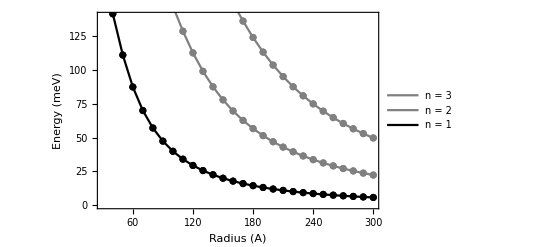

```mathematica
Show[
ListPlot[Table[{rw⟦i⟧,1000*energy⟦i,4⟧},{i,Length[rw]}],PlotStyle-> Gray,Joined->True,Mesh->Full,PlotLegends->{"n = 3"}],
ListPlot[Table[{rw⟦i⟧,1000*energy⟦i,3⟧},{i,Length[rw]}],PlotStyle-> Gray,Joined->True,Mesh->Full,PlotLegends->{"n = 2"}],
ListPlot[Table[{rw⟦i⟧,1000*energy⟦i,2⟧},{i,Length[rw]}],PlotStyle-> Black,Joined->True,Mesh->Full,PlotLegends->{"n = 1"}]
,PlotRange->{0.,140.},Frame->True,FrameLabel-> {"Radius (A)", "Energy (meV)"}]
```

## To Use the same normalization condition as Harrison ( ∫ψ(r)^2 ⅆr) use

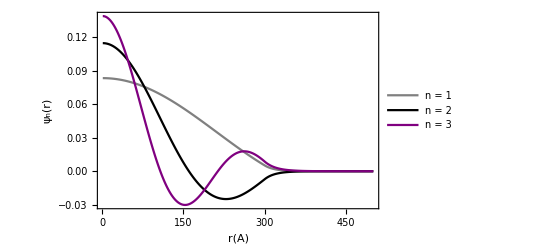

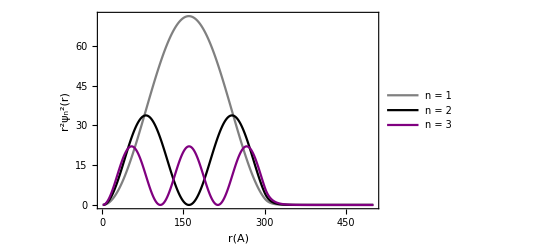

```mathematica
Do[functions1⟦i⟧=functions⟦i⟧/√(functions⟦i⟧.functions⟦i⟧ * dr),{i,3}]
Show[
ListLinePlot[functions1⟦1⟧,PlotRange->All,PlotStyle-> Gray,PlotLegends->{"n = 1"}],
ListLinePlot[functions1⟦2⟧,PlotRange->All,PlotStyle-> Black,PlotLegends->{"n = 2"}],
ListLinePlot[functions1⟦3⟧,PlotRange->All,PlotStyle-> Purple,PlotLegends->{"n = 3"}],
PlotRange-> All,Frame -> True,FrameLabel-> {"r(A)", "ψ_n(r)"} ]
Show[
ListLinePlot[r^2*functions1⟦1⟧^2,PlotRange->All,PlotStyle-> Gray,PlotLegends->{"n = 1"}],
ListLinePlot[r^2*functions1⟦2⟧^2,PlotRange->All,PlotStyle-> Black,PlotLegends->{"n = 2"}],
ListLinePlot[r^2*functions1⟦3⟧^2,PlotRange->All,PlotStyle-> Purple,PlotLegends->{"n = 3"}],
PlotRange-> All,Frame -> True,FrameLabel-> {"r(A)", "r^2ψ_n^2(r)"} ]
```

## To Use Different normalization condition ( ∫ψ(r)^2 r^2 ⅆr) use

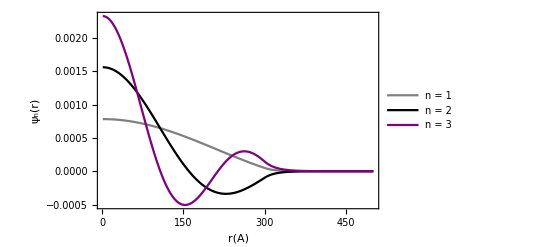

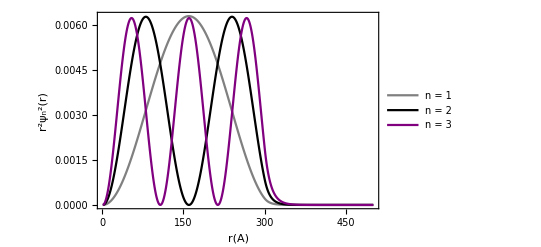

```mathematica
Do[functions2⟦i⟧=functions⟦i⟧/√((functions⟦i⟧*r).(functions⟦i⟧*r) * dr),{i,3}]

Show[
ListLinePlot[functions2⟦1⟧,PlotRange->All,PlotStyle-> Gray,PlotLegends->{"n = 1"}],
ListLinePlot[functions2⟦2⟧,PlotRange->All,PlotStyle-> Black,PlotLegends->{"n = 2"}],
ListLinePlot[functions2⟦3⟧,PlotRange->All,PlotStyle-> Purple,PlotLegends->{"n = 3"}],
PlotRange-> All,Frame -> True,FrameLabel-> {"r(A)", "ψ_n(r)"} ]

Show[
ListLinePlot[r^2*functions2⟦1⟧^2,PlotRange->All,PlotStyle-> Gray,PlotLegends->{"n = 1"}],
ListLinePlot[r^2*functions2⟦2⟧^2,PlotRange->All,PlotStyle-> Black,PlotLegends->{"n = 2"}],
ListLinePlot[r^2*functions2⟦3⟧^2,PlotRange->All,PlotStyle-> Purple,PlotLegends->{"n = 3"}],
PlotRange-> All,Frame -> True,FrameLabel-> {"r(A)", "r^2ψ_n^2(r)"} ]
```